```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Carter\relativistic-aberration\src

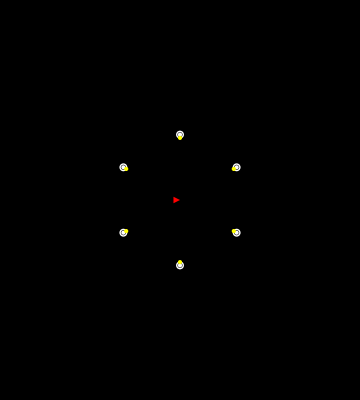
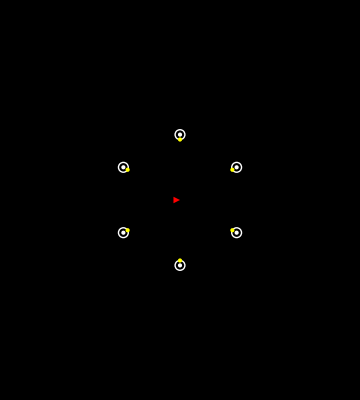
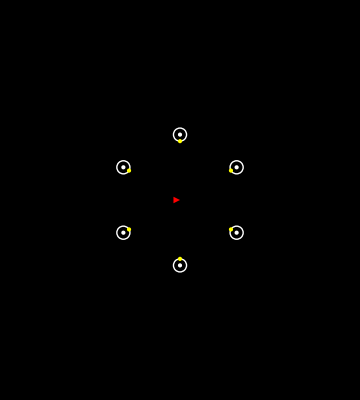
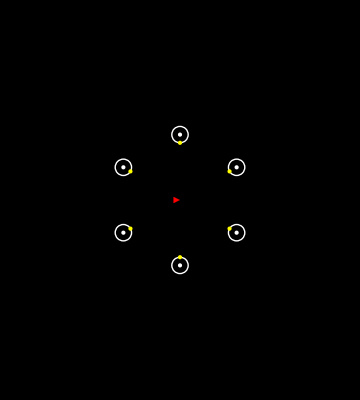
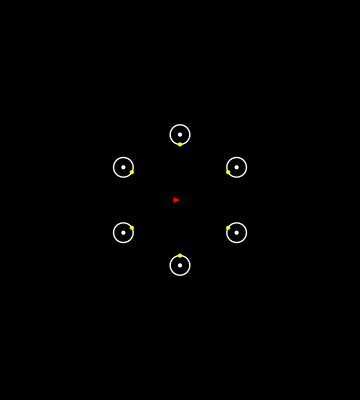
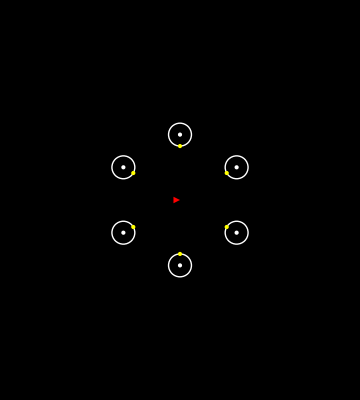
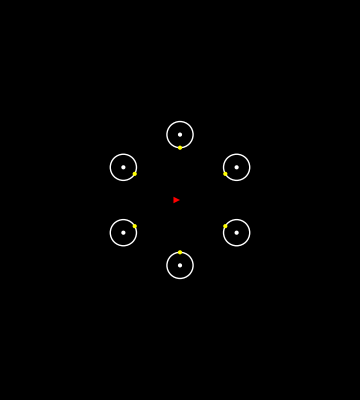
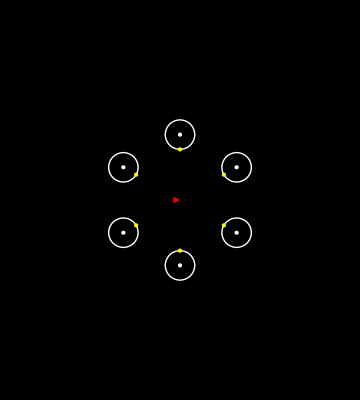
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

stationary.gif

```mathematica
stationary=Table[Graphics[{
White,Point[{{-Sqrt[3],1},{0,2},{Sqrt[3],1},{-Sqrt[3],-1},{0,-2},{Sqrt[3],-1}}],
Red,Triangle[{{-.2,.1},{-.2,-.1},{0,0}}],
White,Circle[{-Sqrt[3],-1},t],Circle[{-Sqrt[3],1},t],Circle[{0,2},t],Circle[{Sqrt[3],1},t],Circle[{Sqrt[3],-1},t],Circle[{0,-2},t],
Yellow,PointSize[Large],Point[{{-Sqrt[3]+t Sqrt[3]/2,-1+t/2},{-Sqrt[3]+t Sqrt[3]/2,1-t/2},{0,2-t},{Sqrt[3]-t Sqrt[3]/2,1-t/2},{Sqrt[3]-t Sqrt[3]/2,-1+t/2},{0,t-2}}],
Black,Point[{{-4.5,0},{4.5,0},{0,5},{0,-5}}]},Background->Black],
{t,0,2,.05}]
Export["stationary.gif",stationary,AnimationRate->10]
```

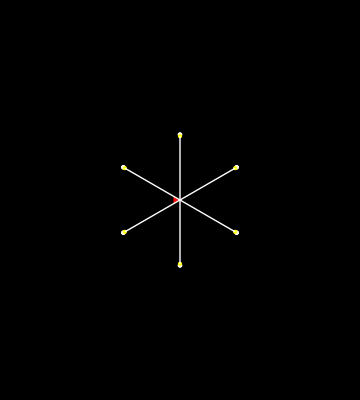
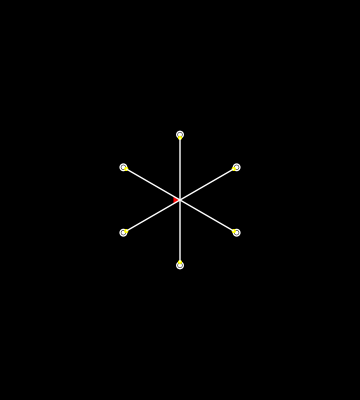
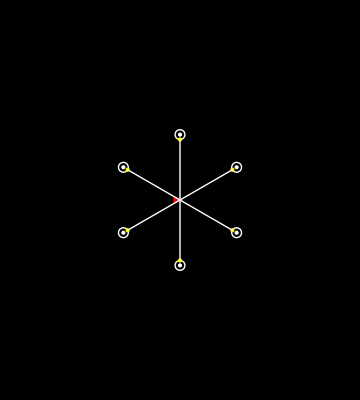
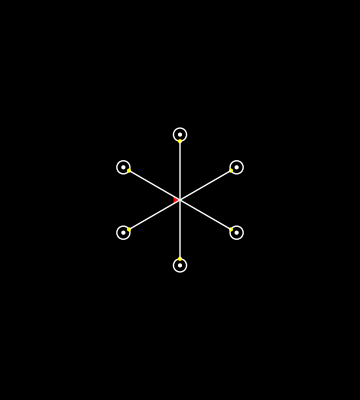
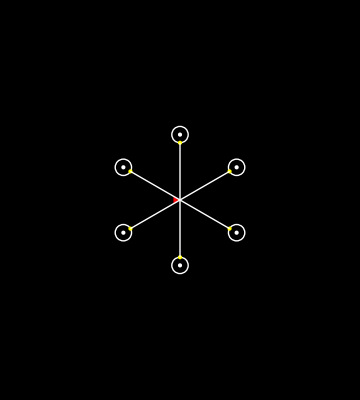
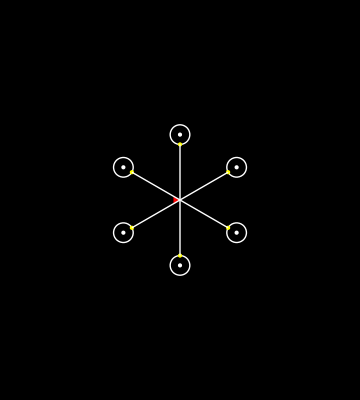
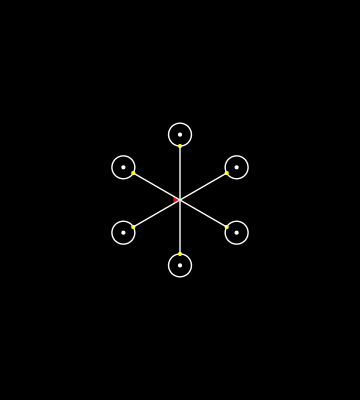
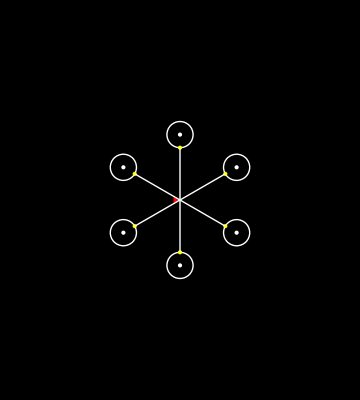
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

stationary2.gif

```mathematica
stationary2=Table[Graphics[{White,Point[{{-Sqrt[3],1},{0,2},{Sqrt[3],1},{-Sqrt[3],-1},{0,-2},{Sqrt[3],-1}}],
Red,Triangle[{{-.2,.1},{-.2,-.1},{0,0}}],
White,Circle[{-Sqrt[3],-1},t],Circle[{-Sqrt[3],1},t],Circle[{0,2},t],Circle[{Sqrt[3],1},t],Circle[{Sqrt[3],-1},t],Circle[{0,-2},t],
Yellow,PointSize[Large],Point[{{-Sqrt[3]+t Sqrt[3]/2,-1+t/2},{-Sqrt[3]+t Sqrt[3]/2,1-t/2},{0,2-t},{Sqrt[3]-t Sqrt[3]/2,1-t/2},{Sqrt[3]-t Sqrt[3]/2,-1+t/2},{0,t-2}}],
Black,Point[{{-4.5,0},{4.5,0},{0,5},{0,-5}}],
White,Line[{{{0,0},{-Sqrt[3]+t Sqrt[3]/2,-1+t/2}},{{0,0},{-Sqrt[3]+t Sqrt[3]/2,1-t/2}},{{0,0},{0,2-t}},{{0,0},{Sqrt[3]-t Sqrt[3]/2,1-t/2}},{{0,0},{Sqrt[3]-t Sqrt[3]/2,-1+t/2}},{{0,0},{0,t-2}}}]},Background->Black],
{t,0,2,.05}]
Export["stationary2.gif",stationary2,AnimationRate->10]
```

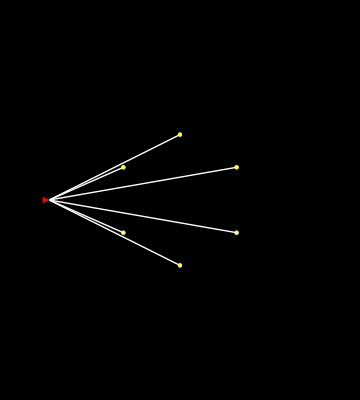
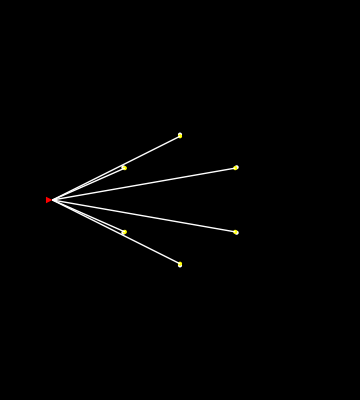
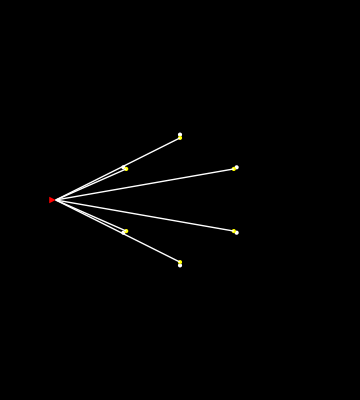
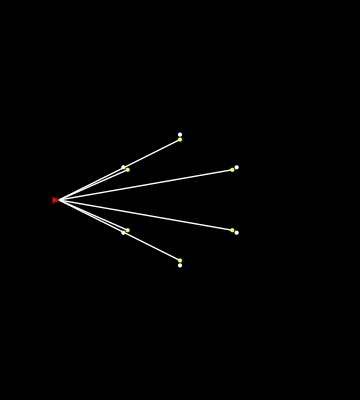
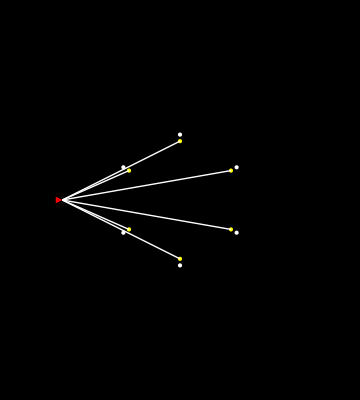
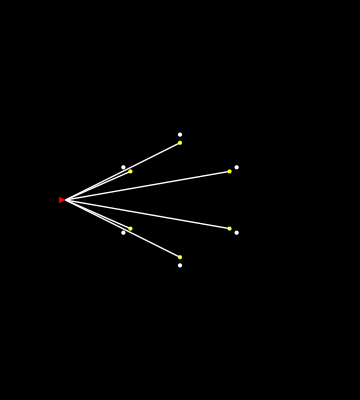
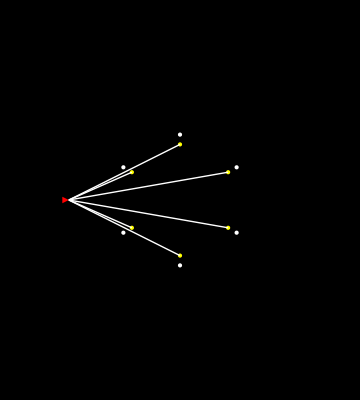
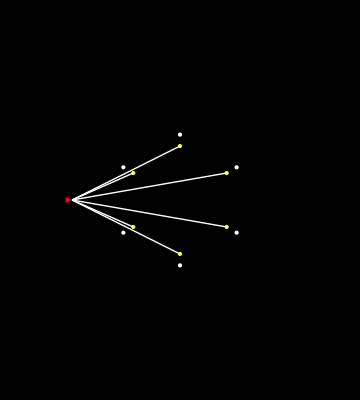
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

classicalMovingDouble.gif

```mathematica
v=2;
classicalMoving=Table[Graphics[{White,Point[{{-Sqrt[3],1},{0,2},{Sqrt[3],1},{-Sqrt[3],-1},{0,-2},{Sqrt[3],-1}}],
Red,Triangle[{{-.2-2v+v t,.1},{-.2-2v+v t,-.1},{-2v+v t,0}}],
Yellow,PointSize[Large],Point[{{-Sqrt[3]+t Sqrt[3]/2,-1+t/2},{-Sqrt[3]+t Sqrt[3]/2,1-t/2},{0,2-t},{Sqrt[3]-t Sqrt[3]/2,1-t/2},{Sqrt[3]-t Sqrt[3]/2,-1+t/2},{0,t-2}}],
Black,Point[{{-4.5,0},{4.5,0},{0,5},{0,-5}}],
White,Line[{{{-2v+v t,0},{-Sqrt[3]+t Sqrt[3]/2,-1+t/2}},{{-2v+v t,0},{-Sqrt[3]+t Sqrt[3]/2,1-t/2}},{{-2v+v t,0},{0,2-t}},{{-2v+v t,0},{Sqrt[3]-t Sqrt[3]/2,1-t/2}},{{-2v+v t,0},{Sqrt[3]-t Sqrt[3]/2,-1+t/2}},{{-2v+v t,0},{0,t-2}}}]},Background->Black],
{t,0,2,.05}]
Export["classicalMovingDouble.gif",classicalMoving,AnimationRate->10]
```

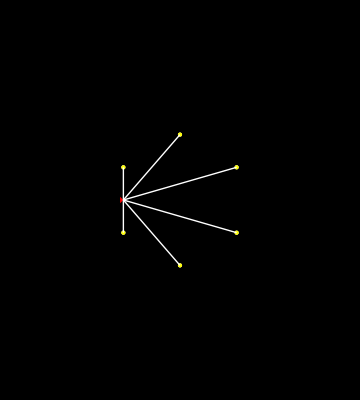
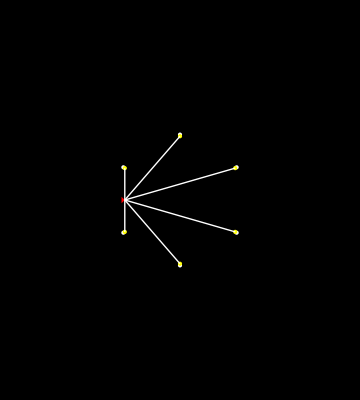
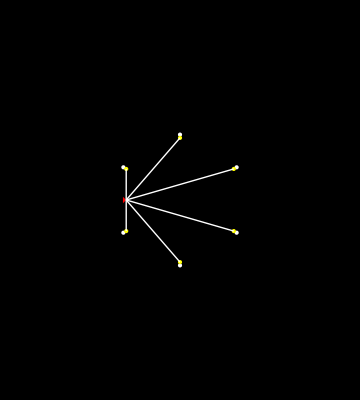
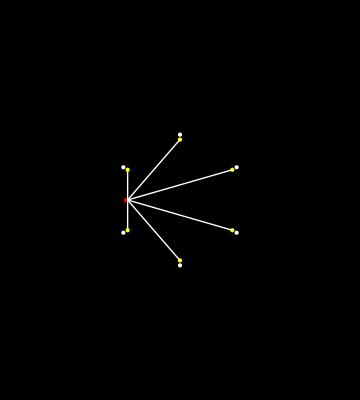
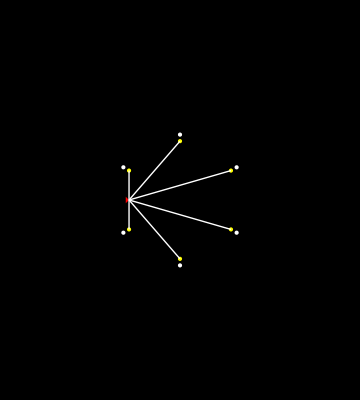
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

shipSquish.gif

```mathematica
v=Sqrt[3]/2;
γ=1/Sqrt[1-v^2];
shipSquish=Table[Graphics[{White,Point[{{-Sqrt[3],1},{0,2},{Sqrt[3],1},{-Sqrt[3],-1},{0,-2},{Sqrt[3],-1}}],
Red,Triangle[{{-.2/γ-2v+v t,.1},{-.2/γ-2v+v t,-.1},{-2v+v t,0}}],
Yellow,PointSize[Large],Point[{{-Sqrt[3]+t Sqrt[3]/2,-1+t/2},{-Sqrt[3]+t Sqrt[3]/2,1-t/2},{0,2-t},{Sqrt[3]-t Sqrt[3]/2,1-t/2},{Sqrt[3]-t Sqrt[3]/2,-1+t/2},{0,t-2}}],
Black,Point[{{-4.5,0},{4.5,0},{0,5},{0,-5}}],
White,Line[{{{-2v+v t,0},{-Sqrt[3]+t Sqrt[3]/2,-1+t/2}},{{-2v+v t,0},{-Sqrt[3]+t Sqrt[3]/2,1-t/2}},{{-2v+v t,0},{0,2-t}},{{-2v+v t,0},{Sqrt[3]-t Sqrt[3]/2,1-t/2}},{{-2v+v t,0},{Sqrt[3]-t Sqrt[3]/2,-1+t/2}},{{-2v+v t,0},{0,t-2}}}]},Background->Black],
{t,0,2,.05}]
Export["shipSquish.gif",shipSquish,AnimationRate->10]
```

```mathematica
v=Sqrt[3]/2;
γ=1/Sqrt[1-v^2];
shipFrame=Table[Graphics[{White,Point[{{γ(-Sqrt[3]-v t),1},{-γ v t,2},{γ(Sqrt[3]-v t),1},{γ(-Sqrt[3]-v t),-1},{-γ v t,-2},{γ(Sqrt[3]-v t),-1}}],
Red,Triangle[{{-.2+γ(-Sqrt[3]),.1},{-.2+γ(-Sqrt[3]),-.1},{γ(-Sqrt[3]),0}}],
Yellow,PointSize[Large],Point[{
{γ(-Sqrt[3])-(γ(t+Sqrt[3]v))(Sqrt[3]/2-v)/(1-Sqrt[3]v/2),1-t/2},
{γ(-Sqrt[3])-(γ(t+Sqrt[3]v))(Sqrt[3]/2-v)/(1-Sqrt[3]v/2),-1+t/2},
{-v γ t,2-t},
{-v γ t, -2+t},
{γ(Sqrt[3]-2v t),1-t/2},
{γ(Sqrt[3]-2v t),-1+t/2}}],
Black,Point[{{-7,0},{4,0}}],
White,Line[{
{{γ(-Sqrt[3]),0},{γ(-Sqrt[3])-(γ(t+Sqrt[3]v))(Sqrt[3]/2-v)/(1-Sqrt[3]v/2),1-t/2}},
{{γ(-Sqrt[3]),0},{γ(-Sqrt[3])-(γ(t+Sqrt[3]v))(Sqrt[3]/2-v)/(1-Sqrt[3]v/2),-1+t/2}},
{{γ(-Sqrt[3]),0},{-v γ t,2-t}},
{{γ(-Sqrt[3]),0},{-v γ t, -2+t}},
{{γ(-Sqrt[3]),0},{γ(Sqrt[3]-2v t),1-t/2}},
{{γ(-Sqrt[3]),0},{γ(Sqrt[3]-2v t),-1+t/2}}
}]
},Background->Black],
{t,0,2,.05}]
Export["shipFrame.gif",shipFrame,AnimationRate->10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

shipFrame.gif